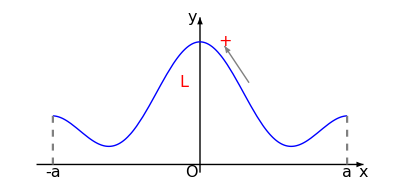

```mathematica
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(********绘图区+坐标系*******)
f1={
Graphics[{
{Black,Arrowheads[0.03],Arrow[{{-2,0},{2,0}}]},
{Black,Arrowheads[0.03],Arrow[{{0,-0.1},{0,1.8}}]},
{Text[Style["x",tF,Italic],{2,-0.1}]},
{Text[Style["y",tF,Italic],{-0.1,1.8}]},
{Text[Style["O",tF,Italic],{-0.1,-0.1}]}
}]
};
(********平面区域*******)
f2={

};
(********平面曲线*******)
f3={
Plot[1-x^2/4+Cos[Pi*x]/2,{x,-1.8,1.8},
AspectRatio->Automatic,PlotStyle->{Blue,Thick}
]
};
(********点+辅助线*******)
f4={
ParametricPlot[{1.8,t},{t,0,1-(1.8)^2/4+Cos[1.8Pi]/2},
PlotStyle->{Dashed,Gray}],
ParametricPlot[{-1.8,t},{t,0,1-(1.8)^2/4+Cos[1.8Pi]/2},
PlotStyle->{Dashed,Gray}]
};
(********文字标记*******)
f5={
Graphics[{
{Text[Style["a",tF,Italic],{1.8,-0.1}]},
{Text[Style["-a",tF,Italic],{-1.8,-0.1}]},
{Text[Style["L",tF,Red,Italic],{-0.2,1}]},
{Text[Style["+",tF,Red],{0.3,1.5}]},
{Gray,Arrowheads[0.03],Arrow[{{0.6,1},{0.3,1.45}}]}
}]
};
Show[f1,f2,f3,f4,f5]
```

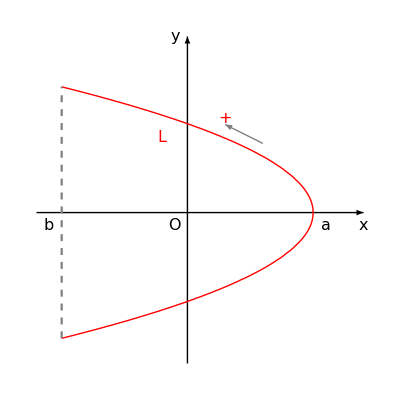

```mathematica
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(********绘图区+坐标系*******)
f1={
Graphics[{
{Black,Arrowheads[0.03],Arrow[{{-1.2,0},{1.4,0}}]},
{Black,Arrowheads[0.03],Arrow[{{0,-1.2},{0,1.4}}]},
{Text[Style["x",tF,Italic],{1.4,-0.1}]},
{Text[Style["y",tF,Italic],{-0.1,1.4}]},
{Text[Style["O",tF,Italic],{-0.1,-0.1}]}
}]
};
(********平面区域*******)
f2={

};
(********平面曲线*******)
f3={
ContourPlot[y^2==1/2-x/2,{x,-1,1},{y,-1,1},
AspectRatio->Automatic,ContourStyle->{Red,Thick}]
};
(********点+辅助线*******)
f4={
ParametricPlot[{-1,t},{t,-1,1},
PlotStyle->{Dashed,Gray}]
};
(********文字标记*******)
f5={
Graphics[{
{Text[Style["a",tF,Italic],{1.1,-0.1}]},
{Text[Style["b",tF,Italic],{-1.1,-0.1}]},
{Text[Style["L",tF,Red,Italic],{-0.2,0.6}]},
{Text[Style["+",tF,Red],{0.3,0.75}]},
{Gray,Arrowheads[0.03],Arrow[{{0.6,0.55},{0.3,0.7}}]}
}]
};
Show[f1,f2,f3,f4,f5]
```